```mathematica
(*20241107: Source cylinder variation and D(1,2) variation; declared variables*)
(*20241010: specified detector counterweight analogous to cylinder; declared variables*)
(*big_G_inputG: additional parameters and updated names*)
(*geometry_input_G: geometry input distributions for big-G version of experiment; updated names*)(*geom_dist_G_20240919: geometry input distributions for big-G version of experiment*)
```

```mathematica
(*clear variables*)
Clear[amp,gap,shape11,shape12,shape13,shape21,shape22,shape23,shape118,shape119,shape120,shape121,shape122,shape123,shape124,shape125,shape216,shape217,shape218,shape219, d1,d2,fstring,x,ux,ushape11,ushape12,ushape13,ushape21,ushape22,ushape23,ushape118,ushape119,ushape120,ushape121,ushape122,ushape123,ushape124,ushape125,ushape216,ushape217,ushape218,ushape219,ud1,ud2,udist,ndist,nv,ne,xru,xrn,xerru,xerrn,pxerru,pxerrn,rpxerru,rpxerrn,rpxerrua,rpxerrna];

(*input*)
(*Central values in microns*)
amp = 30. ;(*source amplitude*)
gap= 100.; (*resting gap*)
shape11=5080.;(*detector x-length*)
shape12=11440.;(*detector y-length*)
shape13=280.;(*detector thickness*)
shape21=10160.;(*source x-length*)
shape22=13440.;(*source y-length*)
shape23=300.;(*source z-length*)
shape118=50.;(*detector mass cylinder radius*)
shape119=100.;(*detector mass cylinder thickness*)
shape120=0.;(*detector mass cylinder x-position*)
shape121=0.;(*detector mass cylinder y-position*)
shape122=50.;(*detector counterweight cylinder radius*)
shape123=100.;(*detector counterweight cylinder thickness*)
shape124=0.;(*detector counterweight x-position*)
shape125=0.;(*detector counterweight y-position*)
shape216=50.;(*source cylinder radius*)
shape217=100.;(*source cylinder thickness*)
shape218 = 0;(*source cylinder x-position*)
shape219 = 0;(*source cylinder y-position*)
d1 = 0;(*test mass separation vector x*)
d2 = 0;(*test mass separation vector y*)

(*uncertainties in microns*)
uamp=6.;(*source amplitude*)
ugap=12.;(*resting gap*)
ushape11=12.;(*detector x-length*)
ushape12=12.;(*detector x-length*)
ushape13=12.;(*detector thickness*)
ushape21=12.;(*source x-length*)
ushape22=12.;(*source x-length*)
ushape23=12.;(*source thickness*)
ushape118=12.;(*detector mass cylinder radius*)
ushape119=12.;(*detector mass cylinder thickness*)
ushape120=12.;(*detector mass cylinder x-position*)
ushape121=12.;(*detector mass cylinder y-position*)
ushape122=12.;(*detector counterweight radius*)
ushape123=12.;(*detector counterweight cylinder thickness*)
ushape124=12.;(*detector counterweight cylinder x-position*)
ushape125=12.;(*detector counterweight y-position*)
ushape216=12.;(*source cylinder radius*)
ushape217=12.;(*source cylinder thickness*)
ushape218=12.;(*source cylinder radius*)
ushape219=12.;(*source cylinder thickness*)
ud1=12.;(*test mass separation vector x*)
ud2=12.;(*test mass separation vector y*)

(*enter output file as string*)
fstring="big_G_input_planck.txt";

(*calculations*)
(*arrays of central values and uncertainties*)
x={amp,gap,shape11,shape12,shape13,shape21,shape22,shape23,shape118,shape119,shape120, shape121, shape122, shape123, shape124, shape125, shape216,shape217,shape218,shape219,d1,d2};
ux={uamp,ugap,ushape11,ushape12,ushape13,ushape21,ushape22,ushape23,ushape118,ushape119,ushape120,ushape121,ushape122,ushape123, ushape124, ushape125, ushape216,ushape217,ushape218,ushape219,ud1,ud2};

(*generate random number distributions*)
udist=UniformDistribution[{-1,1}];
ndist=NormalDistribution[0,1];

(*generate random arrays for each variable with N elements*)
nv=Length[x];(*number of variables*)
ne=1000;(*number of elements*)
SeedRandom[1729];
xru=RandomReal[udist,{ne,nv}];
xrn=RandomReal[ndist,{ne,nv}];

(*add random arrays to central values*)
xerru=Table[x+ux xru[[i]],{i,1,ne}];
xerrn=Table[x+ux xrn[[i]],{i,1,ne}];

(*prepend central values*)
pxerru=Prepend[xerru,x];
pxerrn=Prepend[xerrn,x];

(*set accuracy*)
rpxerru=SetAccuracy[pxerru,3];
rpxerrn=SetAccuracy[pxerrn,3];

(*append extra character to make f77 readable*)
rpxerrua=Append[rpxerru,""];
rpxerrna=Append[rpxerrn,""];

(*export*)
epxerrua=Export["C:\\Users\\jcl\\OneDrive - University of Illinois - Urbana\\long_group\\experiment\\Torsion_Oscillator\\big_G\\sensitivity\\planck\\Github\\single_phase\\masses_on\\"<>fstring,rpxerrua,"Table"];
```

```mathematica
(*transpose arrays for plotting*)
Clear[rpxerrut,rpxerrnt]
rpxerrut=Transpose[rpxerru];
rpxerrnt=Transpose[rpxerrn];
```

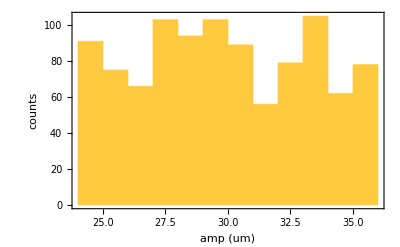

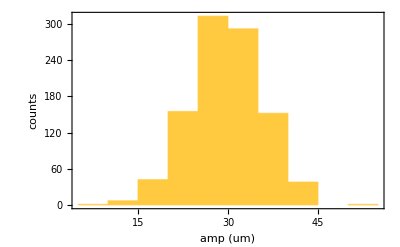

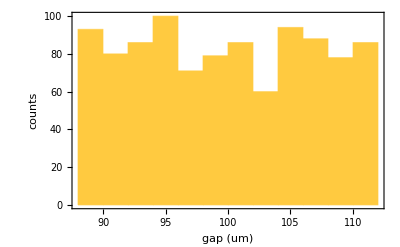

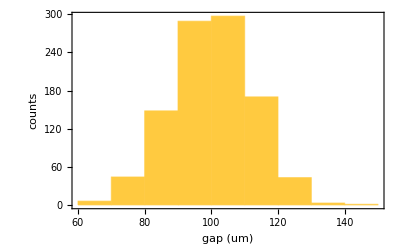

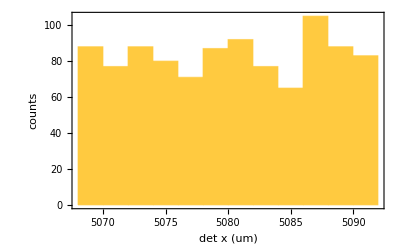

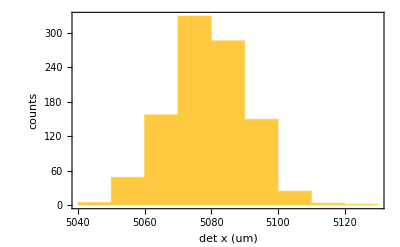

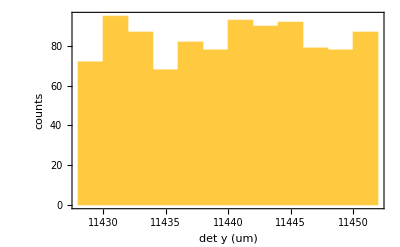

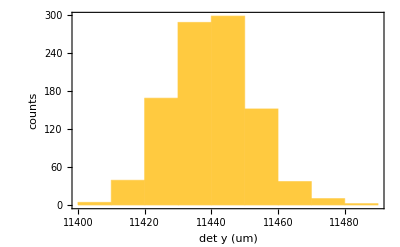

```mathematica
amphistu=Histogram[rpxerrut[[1]],10,Frame->True,FrameLabel->{"amp (um)","counts"}]
amphistn=Histogram[rpxerrnt[[1]],10,Frame->True,FrameLabel->{"amp (um)","counts"}]
gaphistu=Histogram[rpxerrut[[2]],10,Frame->True,FrameLabel->{"gap (um)","counts"}]
gaphistn=Histogram[rpxerrnt[[2]],10,Frame->True,FrameLabel->{"gap (um)","counts"}]
shape11histu=Histogram[rpxerrut[[3]],10,Frame->True,FrameLabel->{"det x (um)","counts"}]
shape11histn=Histogram[rpxerrnt[[3]],10,Frame->True,FrameLabel->{"det x (um)","counts"}]
shape12histu=Histogram[rpxerrut[[4]],10,Frame->True,FrameLabel->{"det y (um)","counts"}]
shape12histn=Histogram[rpxerrnt[[4]],10,Frame->True,FrameLabel->{"det y (um)","counts"}]
shape13histu=Histogram[rpxerrut[[5]],10,Frame->True,FrameLabel->{"det z (um)","counts"}]
shape13histn=Histogram[rpxerrnt[[5]],10,Frame->True,FrameLabel->{"det z (um)","counts"}]
shape21histu=Histogram[rpxerrut[[6]],10,Frame->True,FrameLabel->{"sou x (um)","counts"}]
shape21histn=Histogram[rpxerrnt[[6]],10,Frame->True,FrameLabel->{"sou x (um)","counts"}]
shape22histu=Histogram[rpxerrut[[7]],10,Frame->True,FrameLabel->{"sou y (um)","counts"}]
shape22histn=Histogram[rpxerrnt[[7]],10,Frame->True,FrameLabel->{"sou y (um)","counts"}]
shape23histu=Histogram[rpxerrut[[8]],10,Frame->True,FrameLabel->{"sou z (um)","counts"}]
shape23histn=Histogram[rpxerrnt[[8]],10,Frame->True,FrameLabel->{"sou z (um)","counts"}]
shape118histu=Histogram[rpxerrut[[9]],10,Frame->True,FrameLabel->{"cyl r (um)","counts"}]
shape118histn=Histogram[rpxerrnt[[9]],10,Frame->True,FrameLabel->{"cyl r (um)","counts"}]
shape119histu=Histogram[rpxerrut[[10]],10,Frame->True,FrameLabel->{"cyl thick (um)","counts"}]
shape119histn=Histogram[rpxerrnt[[10]],10,Frame->True,FrameLabel->{"cyl thick (um)","counts"}]
shape120histu=Histogram[rpxerrut[[11]],10,Frame->True,FrameLabel->{"cyl x error (um)","counts"}]
shape120histn=Histogram[rpxerrnt[[11]],10,Frame->True,FrameLabel->{"cyl x error (um)","counts"}]
shape121histu=Histogram[rpxerrut[[12]],10,Frame->True,FrameLabel->{"cyl y error (um)","counts"}]
shape121histn=Histogram[rpxerrnt[[12]],10,Frame->True,FrameLabel->{"cyl y error (um)","counts"}]
shape122histu=Histogram[rpxerrut[[13]],10,Frame->True,FrameLabel->{"counterwt r (um)","counts"}]
shape122histn=Histogram[rpxerrnt[[13]],10,Frame->True,FrameLabel->{"counterwt r (um)","counts"}]
shape123histu=Histogram[rpxerrut[[14]],10,Frame->True,FrameLabel->{"counterwt thick (um)","counts"}]
shape123histn=Histogram[rpxerrnt[[14]],10,Frame->True,FrameLabel->{"counterwt thick (um)","counts"}]
shape124histu=Histogram[rpxerrut[[15]],10,Frame->True,FrameLabel->{"counterwt x error (um)","counts"}]
shape124histn=Histogram[rpxerrnt[[15]],10,Frame->True,FrameLabel->{"counterwt x error (um)","counts"}]
shape125histu=Histogram[rpxerrut[[16]],10,Frame->True,FrameLabel->{"counterwt y error (um)","counts"}]
shape125histn=Histogram[rpxerrnt[[16]],10,Frame->True,FrameLabel->{"counterwt y error (um)","counts"}]
shape216histu=Histogram[rpxerrut[[17]],10,Frame->True,FrameLabel->{"source cyl r (um)","counts"}]
shape217histn=Histogram[rpxerrnt[[17]],10,Frame->True,FrameLabel->{"source cyl r (um)","counts"}]
shape216histu=Histogram[rpxerrut[[18]],10,Frame->True,FrameLabel->{"source cyl thick (um)","counts"}]
shape217histn=Histogram[rpxerrnt[[18]],10,Frame->True,FrameLabel->{"source cyl thick (um)","counts"}]
shape218histu=Histogram[rpxerrut[[19]],10,Frame->True,FrameLabel->{"source cyl x error (um)","counts"}]
shape218histn=Histogram[rpxerrnt[[19]],10,Frame->True,FrameLabel->{"source cyl x error (um)","counts"}]
shape219histu=Histogram[rpxerrut[[20]],10,Frame->True,FrameLabel->{"source cyl y error (um)","counts"}]
shape219histn=Histogram[rpxerrnt[[20]],10,Frame->True,FrameLabel->{"source cyl y error (um)","counts"}]
d1histu=Histogram[rpxerrut[[21]],10,Frame->True,FrameLabel->{"test mass separation x error (um)","counts"}]
d1histn=Histogram[rpxerrnt[[21]],10,Frame->True,FrameLabel->{"test mass separation x error (um)","counts"}]
d2histu=Histogram[rpxerrut[[22]],10,Frame->True,FrameLabel->{"test mass separation y error (um)","counts"}]
d2histn=Histogram[rpxerrnt[[22]],10,Frame->True,FrameLabel->{"test mass separation y error (um)","counts"}]
```